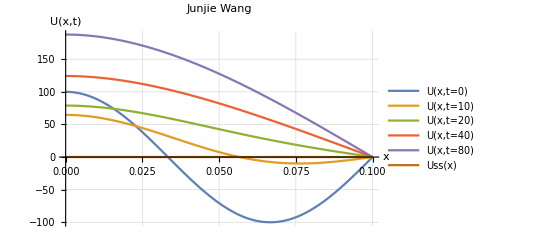

```mathematica
Uss[x_]:=5/(6*6.4*10^5*0.1)x^3-2.5x^2+5*0.01/2-5*0.001/(6*6.4*10^5*0.1)
T=100;
L=0.1;
K=6.4*10^-5;
Q=5;

U[x_,t_]:= Cos[(3π)/(2L)x](((8Q)/(π^2(3)^2))/(K((3π)/(2L))^2)+(T-((8Q)/(π^2(3)^2))/(K((3π)/(2L))^2))ⅇ^(-K((3π)/(2L))^2 t))+∑_(n=3)^10 Cos[((2n-1)π)/(2L)x](((8Q)/(π^2(2n-1)^2))/(K(((2n-1)π)/(2L))^2)-((8Q)/(π^2(2n-1)^2))/(K(((2n-1)π)/(2L))^2)ⅇ^(-K(((2n-1)π)/(2L))^2 t))+Cos[π/(2L)x](((8Q)/π^2)/(K(π/(2L))^2)-((8Q)/π^2)/(K(π/(2L))^2)ⅇ^(-K(π/(2L))^2 t))
Plot[{U[x,t=0],U[x,t=10],U[x,t=20],U[x,t=40],U[x,t=80],Uss[x]},{x,0,0.1},
AxesLabel-> {"x","U(x,t)"},
PlotLabel->"Junjie Wang",
PlotLegends->"Expressions",
GridLines->Automatic,
BaseStyle->{FontSize-> 18}]
```

```mathematica
F[x_,y_]:= (5/Sinh[1.5*Pi])*Sinh[Pi*x]*Cos[Pi*y]
Plot3D[F[x,y],{x,0,1.5},{y,0,1},
PlotRange->Full,
AxesLabel-> {"x","y","T"},
PlotLabel->"Junjie Wang",
BaseStyle->{FontSize-> 18}]
```

-Graphics3D-

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

-Graphics3D-